```mathematica
f[x]==x^2
```

f[x]==x^2

```mathematica
Expand@((2k+1)^2)
```

1+4 k+4 k^2

```mathematica
Expand@((2k)^2)
```

4 k^2

```mathematica
x^2
```

x^2

```mathematica
re[x^2,n]==x^(2n)
```

re[x^2,n]==x^(2 n)

```mathematica
(2k+1)^(2n)
```

(1+2 k)^(2 n)

```mathematica
Expand[(1+2 k)^2]
```

1+4 k+4 k^2

```mathematica
(1+4 k+4 k^2)^n
```

(1+4 k+4 k^2)^n

```mathematica
ExpandAll@((1+4 k+4 k^2)^2)
```

1+8 k+24 k^2+32 k^3+16 k^4

```mathematica
ExpandAll@((1+4 k+4 k^2)^3)
```

1+12 k+60 k^2+160 k^3+240 k^4+192 k^5+64 k^6

```mathematica
x^2+x
```

x+x^2

```mathematica
x^2+x/.x->x^2+x
```

x+x^2+(x+x^2)^2

```mathematica
Expand[x+x^2+(x+x^2)^2]
```

x+2 x^2+2 x^3+x^4

```mathematica
With[{f=#^2+#&},
ExpandAll[f[x]]
]
```

x+x^2

```mathematica
With[{f=#^2+#&,n=2},
ExpandAll[Nest[f,x,n]]
]
```

x+2 x^2+2 x^3+x^4

```mathematica
With[{f=#^2+1&,n=2},
ExpandAll[Nest[f,x,n]]
]
```

2+2 x^2+x^4

```mathematica
D[f[f[x]],x]
```

f'[x] f'[f[x]]

```mathematica
(x^3)(x^2)
```

x^5

```mathematica
(x^3)(x^2)/.x->(x^3)(x^2)
```

x^25

```mathematica
(x^5)^5==(x^3)(x^2)/.x->(x^3)(x^2)
```

x^125==x^25

```mathematica
x^5==(x^3)(x^2)/.x->(x^3)(x^2)
```

True

```mathematica
x^(5 5)==((x^3)(x^2)/.x->(x^3)(x^2))
```

True

```mathematica
x^(α n)
```

x^(n α)

```mathematica
Solve[2x+3==7,x]
```

{{x→2}}

```mathematica
TakeLargestBy[
{#,CountryData[#,"GDPPerCapita"]}&/@CountryData[]
,Last,10]
```

$Aborted[]

$Aborted[]

```mathematica
Grid@
TakeLargestBy[
{#,CountryData[#,"GDPPerCapita"]}&/@CountryData[]
,Last,10]
```

Liechtenstein | 168146. $
Monaco | 163352. $
Luxembourg | 102831. $
Bermuda | 85748.1 $
Isle of Man | 81672. $
Switzerland | 78812.7 $
Macau | 73187. $
Norway | 70812.5 $
Cayman Islands | 64104.8 $
Ireland | 61606.5 $

```mathematica
Composition[Subscript[f, 3],Subscript[f, 2],Subscript[f, 1]][x]
```

f_3[f_2[f_1[x]]]

```mathematica
Composition[D,Subscript[f, 3],Subscript[f, 2],Subscript[f, 1]][x]
```

f_3[f_2[f_1[x]]]

```mathematica
Composition[D[#,x]&,Subscript[f, 3],Subscript[f, 2],Subscript[f, 1]][x]
```

f_1'[x] f_2'[f_1[x]] f_3'[f_2[f_1[x]]]

```mathematica
Composition[1+#&,#^2&][x]
```

1+x^2

```mathematica
f[g[x]]
```

f[g[x]]

```mathematica
f[g[f[g[x]]]]
```

f[g[f[g[x]]]]

```mathematica
h[x]==f[g[x]]
```

h[x]==f[g[x]]

```mathematica
h[h[x]]
```

h[h[x]]

```mathematica
Composition[h][x]
```

h[x]

```mathematica
Composition[h][x]
```

h[x]

```mathematica
Apply[Composition,{h,h,h}][x]
```

h[h[h[x]]]

```mathematica
x+b
```

b+x

```mathematica
Nest[#+b&,x,2]
```

2 b+x

```mathematica
α x^β
```

x^β α

```mathematica
α x^β/.x->α x^β
```

α (x^β α)^β

```mathematica
PowerExpand[α (x^β α)^β]
```

x^(β^2) α^(1+β)

```mathematica
x+2n
```

2 n+x

```mathematica
f[x]==(1-a[x])f[x]+a[x]g[x]
```

f[x]==(1-a[x]) f[x]+a[x] g[x]

```mathematica
x+2n==(1-a[x]) (x+2n)+a[x] g[x]
```

2 n+x==(2 n+x) (1-a[x])+a[x] g[x]

```mathematica
x+2n==(1-a[x]) (x+2n)+a[x] g[x]/.a[x]->((1+Cos[π x])/2)
```

2 n+x==(2 n+x) (1+1/2 (-1-Cos[π x]))+1/2 (1+Cos[π x]) g[x]

```mathematica
2 n+x==(2 n+x) (1+1/2 (-1-Cos[π x]))+1/2 (1+Cos[π x])
```

2 n+x==(2 n+x) (1+1/2 (-1-Cos[π x]))+1/2 (1+Cos[π x])

```mathematica
ExpandAll[2 n+x==(2 n+x) (1+1/2 (-1-Cos[π x]))+1/2 (1+Cos[π x])]
```

2 n+x==1/2+n+x/2+1/2 Cos[π x]-n Cos[π x]-1/2 x Cos[π x]

```mathematica
Solve[2 n+x==1/2+n+x/2+1/2 Cos[π x]-n Cos[π x]-1/2 x Cos[π x],n]
```

{{n→(1-x)/2}}

```mathematica
x
```

x

```mathematica
x-x+x
```

x

```mathematica
x-x+x x
```

x^2

```mathematica
f[x]==x
```

f[x]==x

```mathematica
f[x]-f[x]+x^2 f[x]
```

x^2 f[x]

```mathematica
f[x]-f[x]+f[x]f[x]
```

f[x]^2

```mathematica
Sign[x]
```

Sign[x]

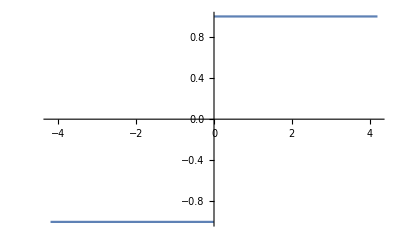

```mathematica
Plot[Sign[x],{x,-4.2,4.2}]
```

```mathematica
(1+Sign[x-4])/2
```

1/2 (1+Sign[-4+x])

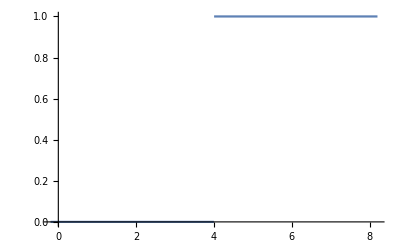

```mathematica
Plot[1/2 (1+Sign[-4+x]),{x,-0.20000000000000018,8.2}]
```

```mathematica
a[x]==(1+Sign[x-4])/2
```

a[x]==1/2 (1+Sign[-4+x])

```mathematica
f[x]==(1-a[x])f[x]+a[x]
```

f[x]==a[x]+(1-a[x]) f[x]

```mathematica
f[x]==a[x]f[x]+1-a[x]
```

f[x]==1-a[x]+a[x] f[x]

```mathematica
-(1+Sign[x-4])/2
```

1/2 (-1-Sign[-4+x])

```mathematica
Simplify[1/2 (-1-Sign[-4+x])]
```

1/2 (-1+Sign[4-x])

```mathematica
(Sign[x-4]-1)/2
```

1/2 (-1+Sign[-4+x])

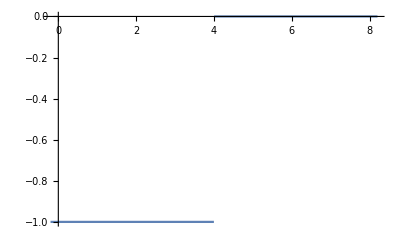

```mathematica
Plot[1/2 (-1+Sign[-4+x]),{x,-0.20000000000000018,8.2}]
```

```mathematica
(1-(1+Sign[x-4])/2)f[x]+(1+Sign[x-4])/2
```

f[x] (1+1/2 (-1-Sign[-4+x]))+1/2 (1+Sign[-4+x])

```mathematica
(1+Sign[x-4])/2 f[x]
```

1/2 f[x] (1+Sign[-4+x])

```mathematica
(1+Sign[x-4])/2(x+n)
```

1/2 (n+x) (1+Sign[-4+x])

```mathematica
(1+Sign[x-4])/2(x+x)
```

x (1+Sign[-4+x])

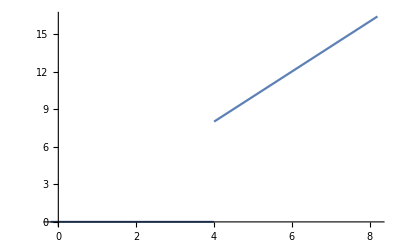

```mathematica
Plot[x (1+Sign[-4+x]),{x,-0.20000000000000018,8.2}]
```

```mathematica
FullSimplify[
Normalize@{1,D[x (1+Sign[-4+x]),x]}.Normalize@{1,2},
x∈Reals]
```

(3+2 Sign[-4+x]+2 x Sign'[-4+x])/(√5 √(1+Abs[1+Sign[-4+x]+x Sign'[-4+x]]^2))

```mathematica
Plot[(3+2 Sign[-4+x]+2 x Sign'[-4+x])/(√5 √(1+Abs[1+Sign[-4+x]+x Sign'[-4+x]]^2))
,{x,-2,10}]
```

-Graphics-

```mathematica
LaplaceTransform[Sin[x],x,s]
```

1/(1+s^2)

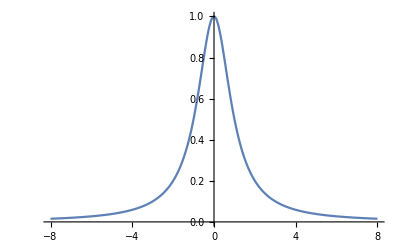

```mathematica
Plot[1/(1+s^2),{s,-8,8}]
```

```mathematica
FourierTransform[Sin[x],x,s]
```

ⅈ √(π/2) DiracDelta[-1+s]-ⅈ √(π/2) DiracDelta[1+s]

```mathematica
LaplaceTransform[2Sin[x],x,s]
```

2/(1+s^2)

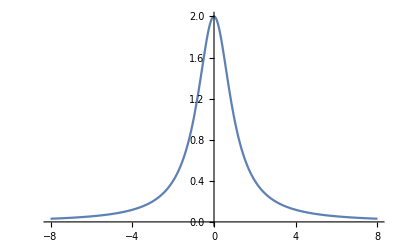

```mathematica
Plot[2/(1+s^2),{s,-8,8}]
```

```mathematica
LaplaceTransform[2Sin[x]+3Cos[x],x,s]
```

(2+3 s)/(1+s^2)

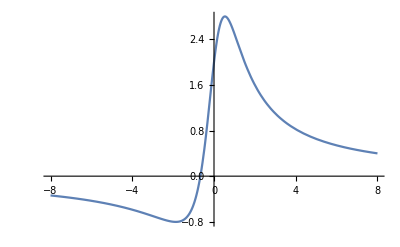

```mathematica
Plot[(2+3 s)/(1+s^2),{s,-8,8}]
```

```mathematica
FourierTransform[2Sin[x]+3Cos[x],x,s]
```

(3+2 ⅈ) √(π/2) DiracDelta[-1+s]+(3-2 ⅈ) √(π/2) DiracDelta[1+s]

```mathematica
(1+Cos[π x])/2
```

1/2 (1+Cos[π x])